SimulationTools > Gravitational Waves

# Gravitational Waves

SimulationTools has a large set of functionality for working with numerical time-series waveforms such as one would obtain by extracting gravitational radiation from a numerical relativity simulation.

## Reading and exporting waveforms

SimulationTools supports a plug-in interface for reading waveform data. The format of choice is HDF5 data using the naming conventions of the Multipole Cactus thorn which is included with the Einstein Toolkit. There is also support for reading waveforms as ASCII data produced by the Multipole thorn and for reading waveforms in the NRDF format [http://arxiv.org/abs/0709.0093].

### Reading data in Multipole format

ReadPsi4 | ReadPsi4Modes | ReadPsi4Radii
$MultipolePsi4Variable |  |

Reading data produced using the Multipole Cactus thorn.

Read in the (2,2) mode of the gravitational waveform from a binary black hole merger, represented by ψ_4 extracted at a radius of 100M

```mathematica
l=2;
m=2;
r=100;
```

```mathematica
ψ4=ReadPsi4[$SimulationToolsTestSimulation,l,m,r]
```

DataTable[<601>,{{0.,300.}}]

It is possible to specify the name of the output file produced by the Multipole thorn using the Multipole::variables parameter in the simulation parameter file, e.g.

Multipole::variables = “WeylScal4::Psi4r{sw=-2 cmplx=’WeylScal4::Psi4i’ name=’psi4’}”

By default, it is assumed that the name ‘psi4’ is used. This may be changed by setting $MultipolePsi4Variable

```mathematica
$MultipolePsi4Variable="psi4";
```

```mathematica
ψ4=ReadPsi4[$SimulationToolsTestSimulation,l,m,r]
```

DataTable[<601>,{{0.,300.}}]

Waveforms can be produced for multiple (l,m) modes and multiple extraction radii. The list of available modes and radii are both easily accessed

```mathematica
ReadPsi4Modes[$SimulationToolsTestSimulation]
```

{{2,-2},{2,-1},{2,0},{2,1},{2,2},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3},{4,-4},{4,-3},{4,-2},{4,-1},{4,0},{4,1},{4,2},{4,3},{4,4},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{6,-6},{6,-5},{6,-4},{6,-3},{6,-2},{6,-1},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,-7},{7,-6},{7,-5},{7,-4},{7,-3},{7,-2},{7,-1},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{8,-8},{8,-7},{8,-6},{8,-5},{8,-4},{8,-3},{8,-2},{8,-1},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8}}

```mathematica
ReadPsi4Radii[$SimulationToolsTestSimulation]//Sort
```

{30.,50.,80.,100.}

### Reading waveforms in other formats

Waveform data from other sources can be imported in a standard ASCII format with three columns corresponding to time and the real and imaginary parts of the waveform

```mathematica
file=FileNameJoin[{$SimulationToolsTestSimulationDirectory,"bbh-nrdf/psi4_l2_m2_r100.00.asc.gz"}];
```

```mathematica
ψ4=ImportWaveform[file]
```

DataTable[<601>,{{0.,300.}}]

### Exporting waveforms

Waveforms can be easily exported as ASCII files

```mathematica
ExportWaveform["/tmp/psi4_l2_m2_r100.00.asc.gz",ψ4]
```

/tmp/psi4_l2_m2_r100.00.asc.gz

## Working with waveforms

### Visualisation

Plot the real and imaginary parts along with the absolute value

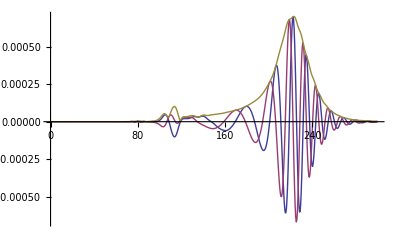

```mathematica
ListLinePlot[{Re[ψ4],Im[ψ4],Abs[ψ4]},PlotRange->All]
```

Plot the phase of the complex waveform

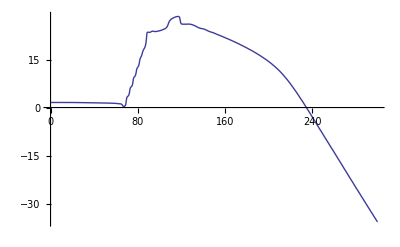

```mathematica
ListLinePlot[Phase[ψ4]]
```

and plot the frequency

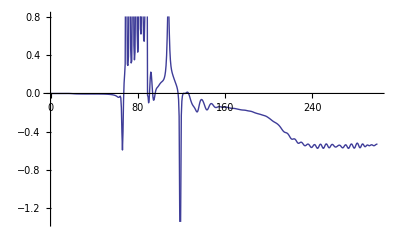

```mathematica
ListLinePlot[Frequency[ψ4]]
```

One frequently would like to know how many gravitational wave cycles are present in a waveform as a measure of its length. The WaveformCycles function does so by counting the number of oscillations from a prescribed time up to the peak of the amplitude, which is assumed to correspond to the merger. In the short example binary black hole simulation, there are approximately three gravitational wave cycles before the merger.

```mathematica
WaveformCycles[ψ4,140]
```

2.97355

It is also possible to obtain this number directly from the simulation, without having to go through the step of reading ψ_4 explicitly

```mathematica
ReadWaveformCycles[$SimulationToolsTestSimulation,140]
```

2.97355

### Manipulating waveforms

#### Aligning phases

It is often convenient to consider a complex waveform in terms of amplitude and phase rather than real and imaginary parts.  When computing the phase, there is a freedom to add multiples of 2π.  When compare two different waveforms, it’s possible that different multiples of 2π have been added to each (this usually happens when the data is not smooth and the algorithm to produce a continuous phase in the Phase function makes a different choice for different waveforms).  The AlignedPhases function adds multiples of 2π to a set of phases to minimise their difference at a specific time.

```mathematica
ψ4r30=Shifted[30ReadPsi4[$SimulationToolsTestSimulation,2,2,30],-30];
ψ4r50=Shifted[50ReadPsi4[$SimulationToolsTestSimulation,2,2,50],-50];
ψ4r80=Shifted[80ReadPsi4[$SimulationToolsTestSimulation,2,2,80],-80];
ψ4r100=Shifted[100ReadPsi4[$SimulationToolsTestSimulation,2,2,100],-100];
```

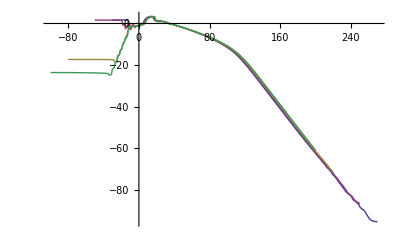

```mathematica
ListLinePlot[AlignedPhases[Phase/@{ψ4r30,ψ4r50,ψ4r80,ψ4r100},70]]
```

#### Converting to strain

Waveforms from numerical relativity simulations are typically extracted as the complex scalar ψ_4, whereas many analytic and data analysis calculations prefer to work with the strain, h, which is related to ψ_4 by two time integrals. The function Psi4ToStrain does this conversion using either fixed-frequency or time-domain integration methods.

Convert ψ_4 to h using fixed-frequency integration

```mathematica
ω0=0.015;
hFFI=Psi4ToStrain[ψ4,ω0];
```

Convert ψ_4 to h using time domain integration chosing the two arbitrary integration constants such that the strain is 0 at t=0 and t=280

```mathematica
hTD=Psi4ToStrain[ψ4,{0,280}];
```

Compare the two integration schemes

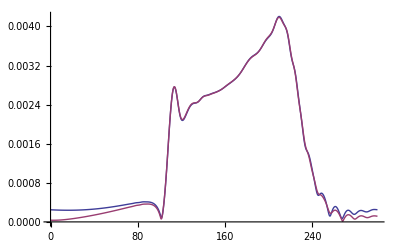

```mathematica
ListLinePlot[Abs[{hFFI,hTD}]]
```

#### Extrapolation

Waveforms from numerical simulations are normally obtained by extraction of ψ_4 at finite radius. However, their definition is in terms of ψ_4 at future null infinity.  It is therefore common to extract at a sequence of radii and extrapolate to infinite radius. SimulationTools provides some automated functions for performing such an extrapolation.

The function ReadRadiallyExtrapolatedPsi4 reads a specific (l,m) mode of ψ_4 at all radii available in a simulation and produces a waveform which has been extrapolated to infinite radius

```mathematica
extrapolationorder=2;
```

```mathematica
ψ4∞=ReadRadiallyExtrapolatedPsi4[$SimulationToolsTestSimulation,l,m,extrapolationorder]
```

DataTable[<461>,{{-30.,200.}}]

We can compare this extrapolated waveform to the one extracted at r=100M

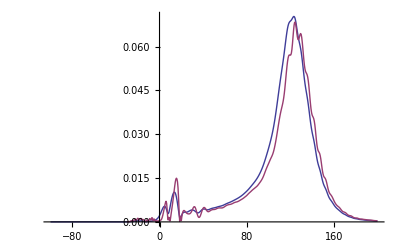

```mathematica
ListLinePlot[Abs[{ψ4r100,ψ4∞}]]
```

One may also wish to compute the strain at future null infinity. This involves a delicate combination of conversion from ψ_4 to strain and extrapolation. The function ReadRadiallyExtrapolatedStrain does this in a way that has been found to be generally robust

```mathematica
h∞=ReadRadiallyExtrapolatedStrain[$SimulationToolsTestSimulation,l,m,ω0,extrapolationorder];
```

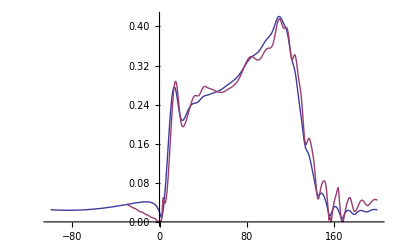

```mathematica
ListLinePlot[Abs[{100Shifted[hFFI,-100],h∞}]]
```

NumericalRelativity

Binaries

BlackHoles

Trackers